```mathematica
ClearAll["Global`*"];

(*args=$CommandLine[[3;;]];
Print[args];
var=ToExpression[args[[2]]];
outputDir=args[[3]];
*)

CB0=1.0; (*mM*)

(*domain values*)
rMin=0.1; (*μm*)
rMax=30; (*μm*)
tMax=200; (*s*)
pts=300;


release = 2*tMax; (* turn off pulsing *)
flat = 0.8; (* homogeneity after illuminated region *)
aOff = 0.8; (* degree of accumulation *)
n =2; (* sharpness of accumulation *)

(*light activation values*)
width=1; (*μm,width of gaussian beam*)
r0=15; (*μm,radius of circle*)
cyc=1;
len=0.25; (*s*)
del=0.025; (*s*)

(*mechanical values*)
λ0=1.6;(*μm^2/s,1st Lame modulus slope*)
μ0=1.6; (*μm^2/s,2nd Lame modulus slope*)
gMin=0.0; (*shrinking factor of activated TCB2*)


(*import functions*)
Get["/Users/csfloyd/Dropbox/Projects/TCB2Network/Mathematica/MidwayFiles/src/TCB2FunctionsND.m"]
```

```mathematica
Manipulate[Plot[f[r,t,0,0.2,4,0.0],{r,rMin,rMax},PlotRange->{0,1}],{t,0,tMax}]
```

```mathematica
ret=AbsoluteTiming[NDSolve[{pdesC,bcs,ics},{u[r,t]},{r,rMin,rMax},{t,0,tMax},Method->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->400,"MaxPoints"->600,"DifferenceOrder"->6},Method->{"IDA","ImplicitSolver"->{"GMRES"}}},PrecisionGoal->6,AccuracyGoal->12,MaxSteps->1000000]];

Print[ret[[1]]];
sol=ret[[2]];
```

NDSolve::eerr: Warning: scaled local spatial error estimate of 34.5425 at t = 200. in the direction of independent variable r is much greater than the prescribed error tolerance. Grid spacing with 401 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

92.8963

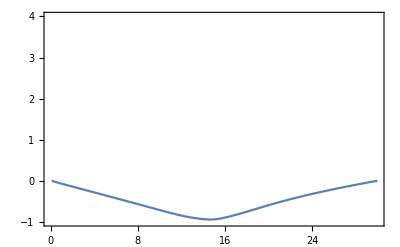

```mathematica
uSol[r_,t_]:=Evaluate[u[r,t]/.sol];
vSol[r_,t_]:=Evaluate[D[uSol[r,tp],tp]/.tp->t];
Plot[{uSol[r,tMax]},{r,rMin,rMax},PlotRange->{-1,4}]
```

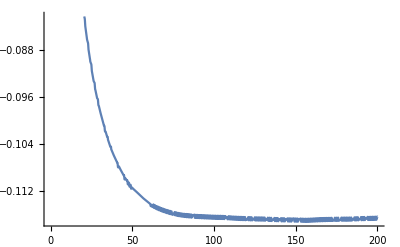

```mathematica
Plot[uSol[5,t],{t,0,tMax}]
```

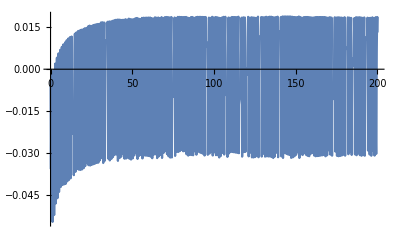

-Graphics-

```mathematica
Plot[vSol[12,t],{t,0,tMax}]
```

```mathematica
tl = 180;
tu = 185;
NIntegrate[vSol[r,t]*gamFunc[r,t]*r,{r,rMin,rMax},{t,tl,tu}, WorkingPrecision->10,Method->{"GlobalAdaptive","MaxErrorIncreases"->2000,Method->"GaussKronrodRule"},MaxRecursion->20] /((tu-tl)*(rMax-rMin))
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{-0.0346338}

{-0.00073618}

{-0.00325205}

```mathematica
Manipulate[Plot[{uSol[r,t],vSol[r,t]},{r,rMin,rMax},PlotRange->{-1,2}],{t,0,tMax}]
```

Plot::plln: Limiting value rMin in {r,rMin,rMax} is not a machine-sized real number.